# Phase diagrams

The coordinates from the previous file “4)Lambda=0.nb” are stored here to make plots:

{0.0432617,0.0385742,0.0338867,0.0293945,0.0250977,0.0209961,0.0172852,0.0139648,0.0110352,0.00869141,0.00712891,0.00576172,0.00478516}

InterpolatingFunction::dmval: Input value {8.17143×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

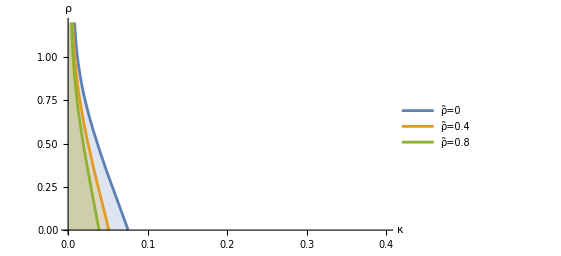

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {8.17143×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
rho={0.,0.1,0.2,0.30000000000000004,0.4,0.5,0.6000000000000001,0.7000000000000001,0.8,0.9,1.,1.1,1.2};
(*rhobar=0*)
kappa1={0.07548828125000001,0.06767578125000001,0.059667968749999994,0.051660156250000006,0.04404296875,0.03681640625000001,0.03017578125,0.024121093750000003,0.01904296875,0.014941406249999999,0.01181640625,0.009667968750000002,0.00810546875};
(*rhobar=0.2*)
kappa2={0.059667968749999994,0.05322265625000001,0.04677734375,0.04052734375000001,0.034472656250000004,0.02880859375,0.02353515625,0.01904296875,0.01513671875,0.01201171875,0.009472656250000001,0.00791015625,0.006542968750000001};
(*rhobar=0.4*)
kappa3 ={0.05126953125000001,0.04599609375,0.04052734375000001,0.03505859375,0.029980468749999996,0.025097656250000003,0.02060546875,0.01669921875,0.013183593750000002,0.010449218750000001,0.00830078125,0.00673828125,0.00576171875};
(*rhobar=0.6*)
kappa4={0.043261718750000004,0.03857421875000001,0.03388671875,0.02939453125,0.025097656250000003,0.02099609375,0.017285156250000003,0.01396484375,0.01103515625,0.00869140625,0.007128906250000001,0.00576171875,0.00478515625}
(*rhobar=0.8*)
kappa5={0.038964843750000006,0.03486328125,0.03076171875,0.026660156250000004,0.022753906250000004,0.01904296875,0.01572265625,0.01259765625,0.010058593750000002,0.00791015625,0.00634765625,0.005175781250000001,0.00439453125};

g1=Interpolation[Transpose[{kappa1,rho}]];
g2=Interpolation[Transpose[{kappa2,rho}]];
g3=Interpolation[Transpose[{kappa3,rho}]];
g4=Interpolation[Transpose[{kappa4,rho}]];
g5=Interpolation[Transpose[{kappa5,rho}]];
Plot[{g1[x],g3[x],g5[x]},{x,0,0.4},Filling->Bottom,PlotRange->{0,1.2},PlotLegends->{"ρ̃=0","ρ̃=0.4","ρ̃=0.8"},AxesLabel->{Style["κ",16,Bold],Style["ρ",16,Bold]}]
```

```mathematica
coords2 ={{0.,0.,1.00048828125},{0.,0.01,1.00927734375},{0.,0.02,1.01806640625},{0.,0.03,1.02392578125},{0.,0.04,1.02978515625},{0.,0.05,1.03564453125},{0.,0.06,1.03857421875},{0.,0.07,1.04150390625},{0.,0.08,1.04150390625},{0.,0.09,1.04150390625},{0.,0.1,1.04150390625},{0.,0.11,1.03857421875},{0.,0.12,1.03564453125},{0.,0.13,1.03271484375},{0.,0.14,1.02685546875},{0.,0.15,1.02099609375},{0.,0.16,1.01513671875},{0.,0.17,1.00634765625},{0.,0.18,0.99755859375},{0.,0.19,0.98583984375},{0.,0.2,0.97705078125},{0.,0.21,0.96240234375},{0.,0.22,0.95068359375},{0.,0.23,0.93603515625},{0.,0.24,0.92138671875},{0.,0.25,0.90380859375},{0.2,0.,1.00048828125},{0.2,0.01,1.00634765625},{0.2,0.02,1.01220703125},{0.2,0.03,1.01806640625},{0.2,0.04,1.02099609375},{0.2,0.05,1.02392578125},{0.2,0.06,1.02685546875},{0.2,0.07,1.02685546875},{0.2,0.08,1.02685546875},{0.2,0.09,1.02392578125},{0.2,0.1,1.02099609375},{0.2,0.11,1.01806640625},{0.2,0.12,1.01220703125},{0.2,0.13,1.00634765625},{0.2,0.14,1.00048828125},{0.2,0.15,0.99169921875},{0.2,0.16,0.98291015625},{0.2,0.17,0.97412109375},{0.2,0.18,0.96240234375},{0.2,0.19,0.95068359375},{0.2,0.2,0.93896484375},{0.2,0.21,0.92431640625},{0.2,0.22,0.90966796875},{0.2,0.23,0.89501953125},{0.2,0.24,0.87744140625},{0.2,0.25,0.85986328125},{0.4,0.,1.00048828125},{0.4,0.01,1.00634765625},{0.4,0.02,1.00927734375},{0.4,0.03,1.01220703125},{0.4,0.04,1.01513671875},{0.4,0.05,1.01513671875},{0.4,0.06,1.01513671875},{0.4,0.07,1.01220703125},{0.4,0.08,1.01220703125},{0.4,0.09,1.00634765625},{0.4,0.1,1.00341796875},{0.4,0.11,0.99755859375},{0.4,0.12,0.99169921875},{0.4,0.13,0.98291015625},{0.4,0.14,0.97412109375},{0.4,0.15,0.96533203125},{0.4,0.16,0.95361328125},{0.4,0.17,0.94189453125},{0.4,0.18,0.93017578125},{0.4,0.19,0.91845703125},{0.4,0.2,0.90380859375},{0.4,0.21,0.88623046875},{0.4,0.22,0.87158203125},{0.4,0.23,0.85400390625},{0.4,0.24,0.83349609375},{0.4,0.25,0.81591796875},{0.6000000000000001,0.,1.00048828125},{0.6000000000000001,0.01,1.00341796875},{0.6000000000000001,0.02,1.00634765625},{0.6000000000000001,0.03,1.00634765625},{0.6000000000000001,0.04,1.00634765625},{0.6000000000000001,0.05,1.00634765625},{0.6000000000000001,0.06,1.00341796875},{0.6000000000000001,0.07,1.00048828125},{0.6000000000000001,0.08,0.99462890625},{0.6000000000000001,0.09,0.99169921875},{0.6000000000000001,0.1,0.98291015625},{0.6000000000000001,0.11,0.97705078125},{0.6000000000000001,0.12,0.96826171875},{0.6000000000000001,0.13,0.95947265625},{0.6000000000000001,0.14,0.94775390625},{0.6000000000000001,0.15,0.93896484375},{0.6000000000000001,0.16,0.92431640625},{0.6000000000000001,0.17,0.91259765625},{0.6000000000000001,0.18,0.89794921875},{0.6000000000000001,0.19,0.88330078125},{0.6000000000000001,0.2,0.86865234375},{0.6000000000000001,0.21,0.85107421875},{0.6000000000000001,0.22,0.83349609375},{0.6000000000000001,0.23,0.81298828125},{0.6000000000000001,0.24,0.79248046875},{0.6000000000000001,0.25,0.77197265625},{0.8,0.,1.00048828125},{0.8,0.01,1.00048828125},{0.8,0.02,1.00048828125},{0.8,0.03,1.00048828125},{0.8,0.04,0.99755859375},{0.8,0.05,0.99462890625},{0.8,0.06,0.99169921875},{0.8,0.07,0.98583984375},{0.8,0.08,0.97998046875},{0.8,0.09,0.97412109375},{0.8,0.1,0.96533203125},{0.8,0.11,0.95654296875},{0.8,0.12,0.94775390625},{0.8,0.13,0.93603515625},{0.8,0.14,0.92431640625},{0.8,0.15,0.90966796875},{0.8,0.16,0.89794921875},{0.8,0.17,0.88330078125},{0.8,0.18,0.86572265625},{0.8,0.19,0.85107421875},{0.8,0.2,0.83349609375},{0.8,0.21,0.81298828125},{0.8,0.22,0.79541015625},{0.8,0.23,0.77490234375},{0.8,0.24,0.75146484375},{0.8,0.25,0.73095703125}};
```

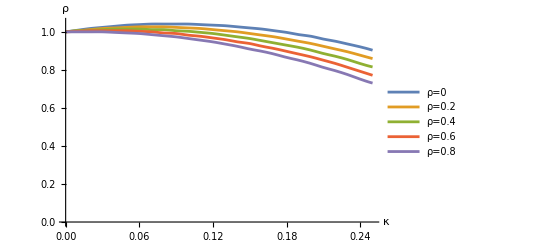

```mathematica
coordinates=coords2; 
x1 = Take[(Transpose[coordinates][[2]]),{1,26}];(*take the first 25 elements of the array defined above, corresponding to ρ̃=0*)
y1 = Take[(Transpose[coordinates][[3]]),{1,26}];
f1= Interpolation[Transpose[{x1,y1}]]; (*interpolate over these coordinates.*)
(*ρ̃=0.2*)
x2 = Take[(Transpose[coordinates][[2]]),{27,52}];
y2 = Take[(Transpose[coordinates][[3]]),{27,52}];
f2 = Interpolation[Transpose[{x2,y2}]];
(*ρ̃=0.4*)
x3 = Take[(Transpose[coordinates][[2]]),{53,78}];
y3 = Take[(Transpose[coordinates][[3]]),{53,78}];
f3 = Interpolation[Transpose[{x3,y3}]];
(*ρ̃=0.6*)
x4 = Take[(Transpose[coordinates][[2]]),{79,104}];
y4 = Take[(Transpose[coordinates][[3]]),{79,104}];
f4= Interpolation[Transpose[{x4,y4}]];
(*ρ̃=0.8*)
x5 = Take[(Transpose[coordinates][[2]]),{105,130}];
y5 = Take[(Transpose[coordinates][[3]]),{105,130}];
f5= Interpolation[Transpose[{x5,y5}]];

Plot[{f1[x],f2[x],f3[x],f4[x],f5[x]},{x,0,0.25},PlotRange->{{0,1.05}},PlotLegends->{"ρ=0","ρ=0.2","ρ=0.4","ρ=0.6","ρ=0.8",},AxesLabel->{Style["κ",15],Style["ρ",15,Bold]}]
```

```mathematica
P=Plot[{f[x],f1[x]},{x,0,0.15},Filling->{1->{{2},{White,LightBlue}}},PlotRange->{0,1.2},PlotLegends->{"First order phase boundary","Topological phase boundary"},AxesLabel->{"κ","ρ"}];
```

## ρ̃=0

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

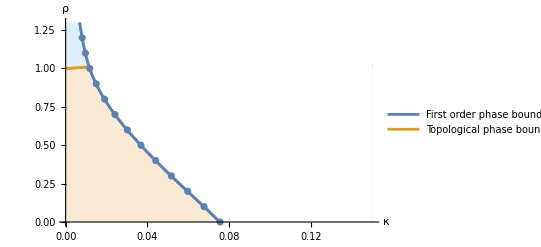

```mathematica
(*point the two phases touch*)
P=Plot[{f[x],f1[x]},{x,0,0.15},Filling->{2->0},FillingStyle->{Lighter},PlotRange->{0,1.3},PlotLegends->{"First order phase boundary","Topological phase boundary"}];(*marks gappless*)
P1=Plot[{f[x],f1[x]},{x,0,0.1},Filling->{1->{{2},{White,LightBlue}}},PlotRange->{0,1.3}];(*marks gapped phase*)
P2=Plot[{f[x]},{x,0,0.15},Filling->{1->2},FillingStyle->White,PlotRange->{0,1.3}];(*Marks Non QSL area white*)
Plotpoints=ListPlot[Transpose[{kappa,rho}]];
Show[P,P1,P2,Plotpoints,AxesLabel->{Style["κ",16,Bold],Style["ρ",16, Bold]}]
```

## ρ̃=0.2

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

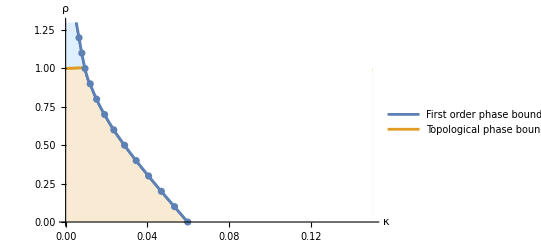

```mathematica
P=Plot[{g2[x],f2[x]},{x,0,0.15},Filling->{2->0},FillingStyle->{Lighter},PlotRange->{0,1.3},PlotLegends->{"First order phase boundary","Topological phase boundary"}];(*marks gappless*)
P1=Plot[{g2[x],f2[x]},{x,0,0.1},Filling->{1->{{2},{White,LightBlue}}},PlotRange->{0,1.3}];(*marks gapped phase*)
P2=Plot[{g2[x]},{x,0,0.15},Filling->{1->2},FillingStyle->White,PlotRange->{0,1.3}];(*Marks Non QSL area white*)
Plotpoints=ListPlot[Transpose[{kappa2,rho}]];
Show[P,P1,P2,Plotpoints,AxesLabel->{Style["κ",16,Bold],Style["ρ",16, Bold]}]
```

## ρ̃=0.4

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

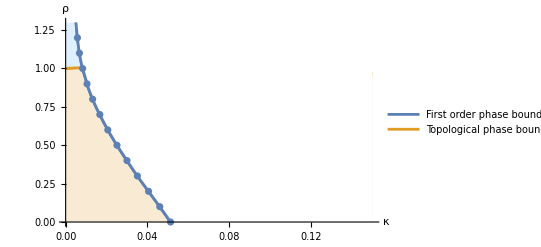

```mathematica
P=Plot[{g3[x],f3[x]},{x,0,0.15},Filling->{2->0},FillingStyle->{Lighter},PlotRange->{0,1.3},PlotLegends->{"First order phase boundary","Topological phase boundary"}];(*marks gappless*)
P1=Plot[{g3[x],f3[x]},{x,0,0.1},Filling->{1->{{2},{White,LightBlue}}},PlotRange->{0,1.3}];(*marks gapped phase*)
P2=Plot[{g3[x]},{x,0,0.15},Filling->{1->2},FillingStyle->White,PlotRange->{0,1.3}];(*Marks Non QSL area white*)
Plotpoints=ListPlot[Transpose[{kappa3,rho}]];
Show[P,P1,P2,Plotpoints,AxesLabel->{Style["κ",16,Bold],Style["ρ",16, Bold]}]
```

## ρ̃=0.6

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

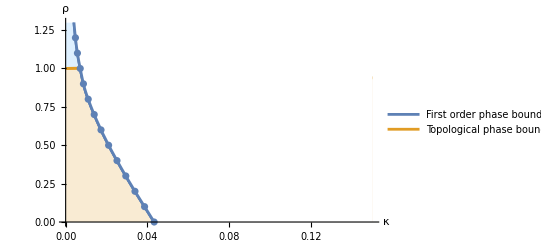

```mathematica
P=Plot[{g4[x],f4[x]},{x,0,0.15},Filling->{2->0},FillingStyle->{Lighter},PlotRange->{0,1.3},PlotLegends->{"First order phase boundary","Topological phase boundary"}];(*marks gappless*)
P1=Plot[{g4[x],f4[x]},{x,0,0.1},Filling->{1->{{2},{White,LightBlue}}},PlotRange->{0,1.3}];(*marks gapped phase*)
P2=Plot[{g4[x]},{x,0,0.15},Filling->{1->2},FillingStyle->White,PlotRange->{0,1.3}];(*Marks Non QSL area white*)
Plotpoints=ListPlot[Transpose[{kappa4,rho}]];
Show[P,P1,P2,Plotpoints,AxesLabel->{Style["κ",16,Bold],Style["ρ",16, Bold]}]
```

## ρ̃=0.8

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.06429×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

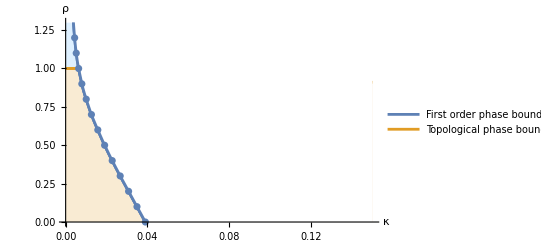

```mathematica
P=Plot[{g5[x],f5[x]},{x,0,0.15},Filling->{2->0},FillingStyle->{Lighter},PlotRange->{0,1.3},PlotLegends->{"First order phase boundary","Topological phase boundary"}];(*marks gappless*)
P1=Plot[{g5[x],f5[x]},{x,0,0.1},Filling->{1->{{2},{White,LightBlue}}},PlotRange->{0,1.3}];(*marks gapped phase*)
P2=Plot[{g5[x]},{x,0,0.15},Filling->{1->2},FillingStyle->White,PlotRange->{0,1.3}];(*Marks Non QSL area white*)
Plotpoints=ListPlot[Transpose[{kappa5,rho}]];
Show[P,P1,P2,Plotpoints,AxesLabel->{Style["κ",16,Bold],Style["ρ",16, Bold]}]
```